```mathematica
ZrC phonon DOS analysis;
```

```mathematica
ClearAll;
```

```mathematica
Examining six volumes from a =4.575to 4.850Ångstrom;
Calculate ZPEs and Grüneisen parameters;
```

Set::write: Tag Times in a Examining from six {95.7576,102.832,105.824,107.782,110.661,114.084} is Protected.

```mathematica
Units/definitions;
```

```mathematica
(*UNITS,
phonon Data read in in THz,
Converted to meV by 1THz=4.14meV,
Convert temperature from Kelvin to meV via 1K=8.6173324*10^-5eV,
2by2by2 supercell 64 atoms
*)
ClearAll;
THz2meV = 4.14;
K2meV=0.086173324;
Natoms=64;
```

```mathematica
Import data - normal total phonon DOS;
```

alatts:

{4.575,4.685,4.73,4.759,4.801,4.85}

Volumes:

{95.7576,102.832,105.824,107.782,110.661,114.084}

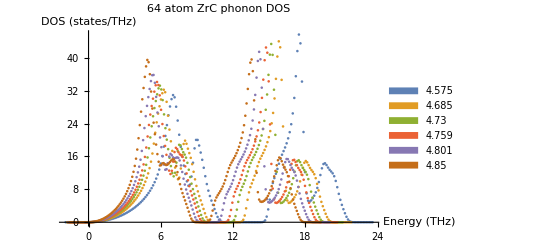

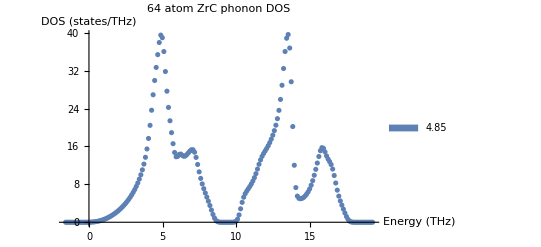

201

```mathematica
(*Import the harmonic phonon DOS*)

SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
filesDOS={"total_dos_4575.dat","total_dos_4685.dat","total_dos_4730.dat","total_dos_4759.dat","total_dos_4801.dat","total_dos_4850.dat"};
"alatts:"
alatts={4.575,4.685,4.730,4.759,4.801,4.850}
"Volumes:"
volumes=alatts^3
phononDOSdata4575=ReadList[filesDOS[[1]],{Number, Number}];
phononDOSdata4685=ReadList[filesDOS[[2]],{Number, Number}];
phononDOSdata4730=ReadList[filesDOS[[3]],{Number, Number}];
phononDOSdata4759=ReadList[filesDOS[[4]],{Number, Number}];
phononDOSdata4801=ReadList[filesDOS[[5]],{Number, Number}];
phononDOSdata4850=ReadList[filesDOS[[6]],{Number, Number}];
phononDOSdataAll={phononDOSdata4575,phononDOSdata4685,phononDOSdata4730,phononDOSdata4759,phononDOSdata4801,phononDOSdata4850};
ListPlot[phononDOSdataAll,AxesLabel->{"Energy\n (THz)","DOS (states/THz)"},PlotLabel->"64 atom ZrC phonon DOS",PlotLegends->Placed[SwatchLegend[ Table[alatts[[i]],{i,1,6}]],{0.92,0.6}]]
ListPlot[phononDOSdataAll[[6]],AxesLabel->{"Energy\n (THz)","DOS (states/THz)"},PlotLabel->"64 atom ZrC phonon DOS",PlotLegends->Placed[SwatchLegend[ Table[alatts[[i]],{i,6,6}]],{0.92,0.6}]]
length=Length[phononDOSdataAll[[1]]]
```

```mathematica
Interpolate data;
```

```mathematica
(*Definie minimum and maximum phonon energies, in THz and meV, and Interpolate the discete phonon data to make function for later analysis*)
"Minimum phonon energy in THz (nb, DOS below zero is practically negligible:"
EminTHz=0
"Minimum phonon energy in meV (nb, DOS below zero is practically negligible:"
Emin=EminTHz*THz2meV
"Maximum phonon enegry in THz:"
EmaxTHz=phononDOSdataAll[[1]][[length,1]]
"Maximum phonon enegry in meV:"
Emax=EmaxTHz*THz2meV
interpolDOS=Table[Interpolation[phononDOSdataAll[[i]]],{i,1,6}];
```

Minimum phonon energy in THz (nb, DOS below zero is practically negligible:

0

Minimum phonon energy in meV (nb, DOS below zero is practically negligible:

0.

Maximum phonon enegry in THz:

23.5739

Maximum phonon enegry in meV:

97.5961

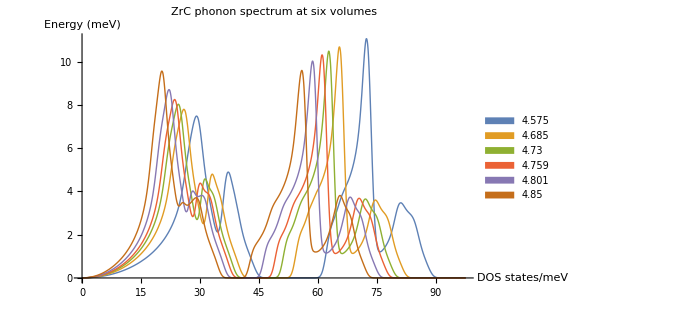

DOS vs volume is quite interesting: 
1)As the temperature increases, volume increases, the Zr (lower) band moves down. The weight of the main peak increases, but no mixing of the between the bands occurs, must just be due to a squeezing of the Zr band into a narrower band. 
2)High weight narrow bands at low energy, that occur at high volume, will have larger phonon entropy than wider more spread out band at high energy (small volume)
3)Is there an analogy with Hubbard bands - Narrow bands are strongly localised in real space, wide bands are real space delocalised.

```mathematica
Plot[Evaluate@Table[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV],{i,1,6}],{energy,0,Emax},PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"},PlotLegends->Placed[SwatchLegend[ Table[SetPrecision[alatts[[i]],4],{i,1,6}]],{0.88,0.6}],PlotLabel->"ZrC phonon spectrum at six volumes"]
"DOS vs volume is quite interesting: 
1)As the temperature increases, volume increases, the Zr (lower) band moves down. The weight of the main peak increases, but no mixing of the between the bands occurs, must just be due to a squeezing of the Zr band into a narrower band. 
2)High weight narrow bands at low energy, that occur at high volume, will have larger phonon entropy than wider more spread out band at high energy (small volume)
3)Is there an analogy with Hubbard bands - Narrow bands are strongly localised in real space, wide bands are real space delocalised."
```

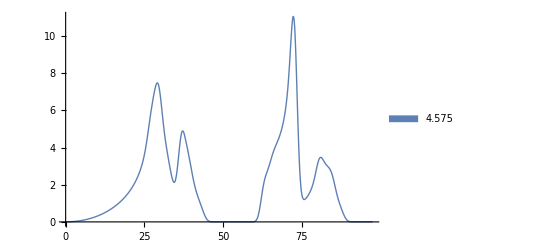

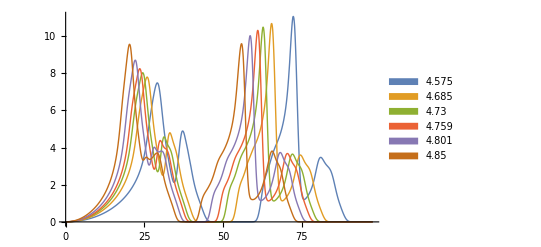

```mathematica
Plot[Evaluate@Table[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV],{i,1,1}],{energy,0,Emax},PlotStyle->Thick,ImageSize->400,PlotLegends->Placed[SwatchLegend[ Table[alatts[[i]],{i,1,6}]],{0.96,0.6}]]
Plot[Evaluate@Table[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV],{i,1,6}],{energy,0,Emax},PlotStyle->Thick,ImageSize->400,PlotLegends->Placed[SwatchLegend[ Table[alatts[[i]],{i,1,6}]],{0.96,0.6}]]
```

```mathematica
Check number of phonon modes equal to 3n;
```

```mathematica
(*Total number of phonon states for each volume*)
Nmodes=Table[NIntegrate[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV],{energy,Emin,Emax}],{i,1,6}]
```

{192.,191.999,191.999,191.999,191.999,191.999}

```mathematica
Zero point energy (ZPE);
```

```mathematica
(*ZPE for each volume*)
zpeAllVol=Table[NIntegrate[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV]*(energy)*0.5/Natoms,{energy,Emin,Emax}],{i,1,6}]
```

{77.2712,69.6775,66.6147,64.6525,61.8201,58.5219}

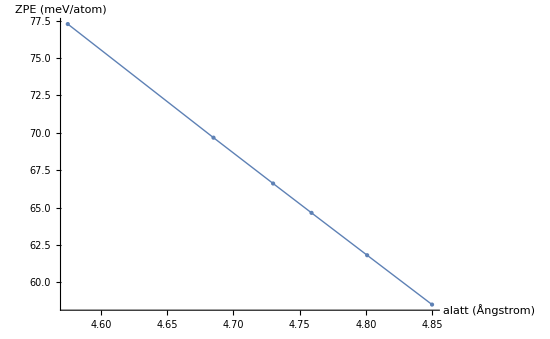

{4.575,4.685,4.73,4.759,4.801,4.85}

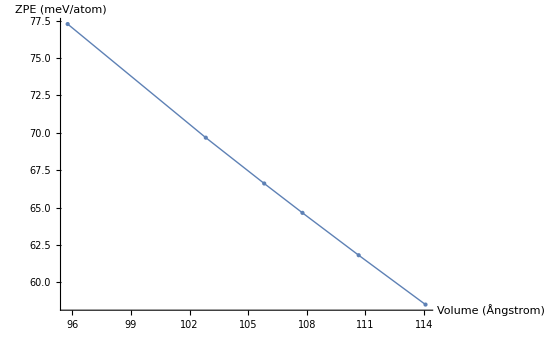

{95.7576,102.832,105.824,107.782,110.661,114.084}

```mathematica
(*Show zero point energy for each lattice parameter and volume*)
plotlabels0={AxesLabel->{"alatt \n (Ångstrom)","ZPE \n (meV/atom)"},PlotStyle->Thick,ImageSize->550};
plotlabels1={AxesLabel->{"Volume \n (Ångstrom)","ZPE \n (meV/atom)"},PlotStyle->Thick,ImageSize->550};
Show[ListPlot[Transpose@{alatts,zpeAllVol},Joined->True,plotlabels0],ListPlot[Transpose@{alatts,zpeAllVol},PlotStyle->PointSize[Large]]]
alatts
Show[ListPlot[Transpose@{volumes,zpeAllVol},Joined->True,plotlabels1],ListPlot[Transpose@{volumes,zpeAllVol},PlotStyle->PointSize[Large]]]
volumes
```

```mathematica
zpeFit=Fit[Transpose@{volumes,zpeAllVol},{1,x,x^2,x^3},x]
```

291.854-3.92136 x+0.0233191 x^2-0.000060256 x^3

```mathematica
Lower band (Zr) band centre energy for each a latt;
```

```mathematica
(*Find the lower band Einstein frequency of each volume DOS*)
(*The lower band in each DOS is Zr, and upper band C*)
(*Einstein frequency defined for lower and upper bands as the energy after which 48 states are counted, from the band starting edge (there is 96 states for each Zr)*)
```

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
listBand1Centre=Table[medianLowerBand/.FindRoot[NIntegrate[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV],{energy,Emin,medianLowerBand}]-48==0,{medianLowerBand,1}],{i,1,6}]
```

{29.5685,26.3295,24.9432,24.0211,22.6334,20.9082}

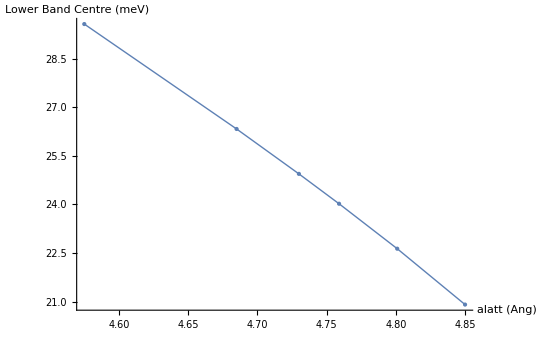

```mathematica
plotlabels2={AxesLabel->{"alatt (Ang)","Lower Band Centre \n (meV)"},ImageSize->550,PlotStyle->Thick};
Show[ListPlot[Transpose@{alatts,listBand1Centre},Joined->True,plotlabels2],ListPlot[Transpose@{alatts,listBand1Centre},PlotStyle->PointSize[Large]]]
```

```mathematica
bandzrFit=Fit[Transpose@{volumes,listBand1Centre},{1,x,x^2,x^3,x^4,x^5},x]
Table[{D[bandzrFit,x]/.x->i/20+4.5,i/20+4.5},{i,1,10}]
bandzrFitLinear=Fit[Transpose@{volumes,listBand1Centre},{1,x,x^2},x]
Table[{D[bandzrFitLinear,x]/.x->(i/20+4.5),i/20+4.5},{i,1,10}]
```

1449.61-66.6152 x+1.27712 x^2-0.0123838 x^3+0.0000603587 x^4-1.18374×10^-7 x^5

{{-55.74,4.55},{-55.6286,4.6},{-55.5173,4.65},{-55.4062,4.7},{-55.2952,4.75},{-55.1844,4.8},{-55.0738,4.85},{-54.9634,4.9},{-54.8531,4.95},{-54.743,5.}}

57.7978-0.146619 x-0.00154813 x^2

{{-0.160707,4.55},{-0.160862,4.6},{-0.161017,4.65},{-0.161171,4.7},{-0.161326,4.75},{-0.161481,4.8},{-0.161636,4.85},{-0.161791,4.9},{-0.161946,4.95},{-0.1621,5.}}

```mathematica
Lower band (Zr) Einstein energy vs volume and Grüneisen;
```

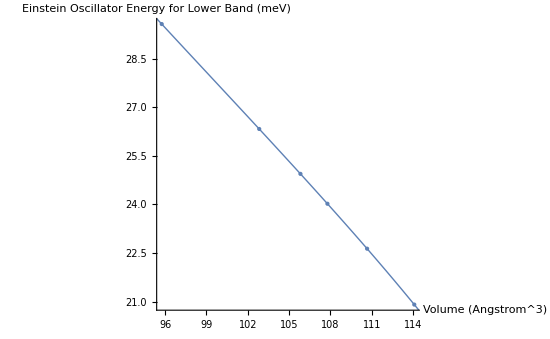

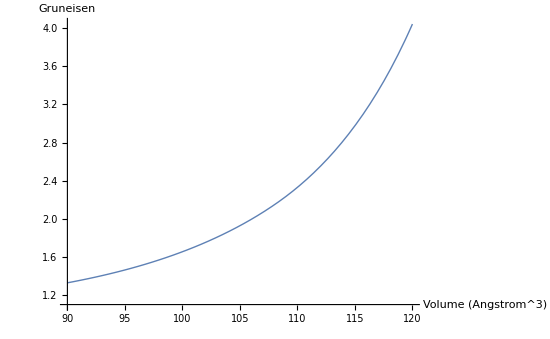

```mathematica
Off[InterpolatingFunction::dmval]
interListBand1Centre=Interpolation[Transpose@{volumes,listBand1Centre},Method->"Spline"];
Show[ListPlot[Transpose@{volumes,listBand1Centre},PlotStyle->{Thick,PointSize[Large]},ImageSize->550,AxesLabel->{"Volume \n(Angstrom^3)", "Einstein Oscillator Energy\n for Lower Band \n (meV)"}],
Plot[{interListBand1Centre[vol],gruneisenBand1[vol]},{vol,90,120},ImageSize->550,PlotStyle->Thick]]
(*Gruneisen defined as Einstein oscillator energy derivative wrt volume,
times minus volume divided by energy,
i.e, -(V/E)(dE/dV)*)
Plot[-(vol/interListBand1Centre[vol])*interListBand1Centre'[vol],{vol,90,120},AxesOrigin->{90,1.1},AxesLabel->{"Volume \n (Angstrom^3)", Gruneisen},ImageSize->550,PlotStyle->Thick]
```

```mathematica
Upper band (carbon) band centre energy for each a latt;
```

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
(*The DOS for each volume is quite different,
so define Emin, Emax, and a half way point,
have to be defined individually for each point*)
"Emin for each volume DOS:"
varEmax=Table[phononDOSdataAll[[i]][[length,1]]*THz2meV,{i,1,6}]
"Emax for each volume DOS:"
varEmin=Table[phononDOSdataAll[[i]][[1,1]]*THz2meV,{i,1,6}]
"Rough energy centre estimate for each volume DOS:"
varBand2Centre=0.5(varEmax-varEmin)
"Upper band (C) band centre calculated counting up to hald the band modes (48):"
listBand2Centre=Table[medianUpperBand/.FindRoot[NIntegrate[(1/THz2meV)*interpolDOS[[i]][energy/THz2meV],{energy,varBand2Centre[[i]],medianUpperBand}]-48==0,{medianUpperBand,60}],{i,1,6}]
```

Emin for each volume DOS:

{97.5961,90.2548,87.332,85.4743,82.817,79.7683}

Emax for each volume DOS:

{-7.86428,-7.32366,-7.10878,-6.97253,-6.778,-6.55634}

Rough energy centre estimate for each volume DOS:

{52.7302,48.7892,47.2204,46.2234,44.7975,43.1623}

Upper band (C) band centre calculated counting up to hald the band modes (48):

{72.1665,65.188,62.4499,60.7228,58.271,55.5724}

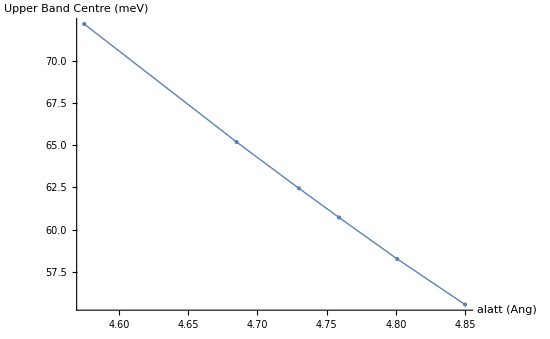

```mathematica
plotlabels3={AxesLabel->{"alatt (Ang)","Upper Band Centre \n (meV)"},ImageSize->550,PlotStyle->Thick};
Show[ListPlot[Transpose@{alatts,listBand2Centre},Joined->True,plotlabels3,PlotStyle->Thick],ListPlot[Transpose@{alatts,listBand2Centre},PlotStyle->PointSize[Large]]]
```

```mathematica
Upper band (C) Einstein energy vs volume and Grüneisen;
```

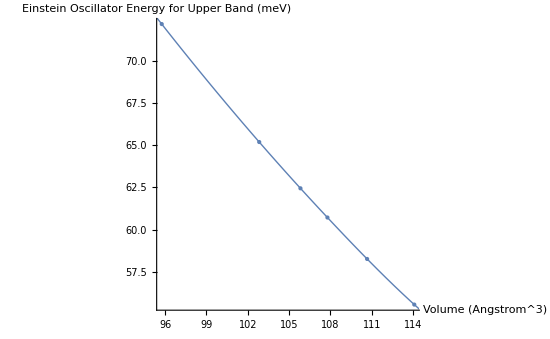

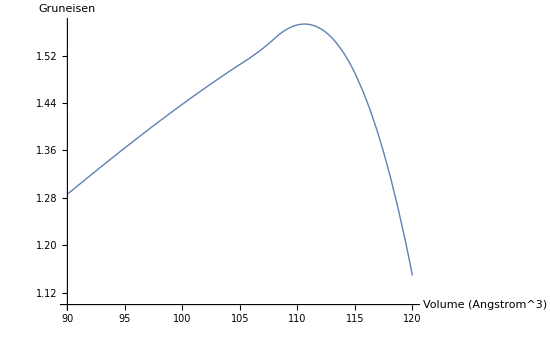

```mathematica
Off[InterpolatingFunction::dmval]
interListBand2Centre=Interpolation[Transpose@{volumes,listBand2Centre},Method->"Spline"];
Show[ListPlot[Transpose@{volumes,listBand2Centre},PlotStyle->{Thick,PointSize[Large]},ImageSize->550,AxesLabel->{"Volume \n(Angstrom^3)", "Einstein Oscillator Energy\n for Upper Band \n (meV)"}],
Plot[{interListBand2Centre[vol],gruneisenBand2[vol]},{vol,90,120},ImageSize->550,PlotStyle->Thick]]
(*Gruneisen as Einstein oscillator energy derivatire wrt volume,
times minus volume divided by energy*)
Plot[-(vol/interListBand2Centre[vol])*interListBand2Centre'[vol],{vol,90,120},AxesOrigin->{90,1.1},AxesLabel->{"Volume \n (Angstrom^3)", Gruneisen},ImageSize->550,PlotStyle->Thick]
```

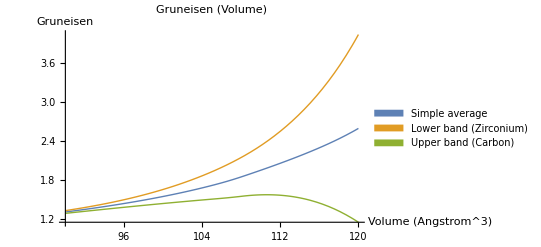

Does this make sense? 
1) Plot say the rate at which the centre of mass (in energy) of the lower Zr band is decreasing, is getting bigger as the volume increases. 
1b) What is the simple physical interpretation: 
2) Zr and C both have same Gruneisen at low vol. 
3) Overall Gruneisen is relatively steady, Zr and C diverge relatively
4)

```mathematica
Plot[{-0.5*(vol/interListBand1Centre[vol])*interListBand1Centre'[vol]+-0.5*(vol/interListBand2Centre[vol])*interListBand2Centre'[vol],-(vol/interListBand1Centre[vol])*interListBand1Centre'[vol],-(vol/interListBand2Centre[vol])*interListBand2Centre'[vol]},{vol,90,120},ImageSize->400,PlotStyle->Thick,AxesLabel->{"Volume \n (Angstrom^3)", Gruneisen},PlotLegends->Placed[SwatchLegend[{"Simple average","Lower band (Zirconium)","Upper band (Carbon)"}],{0.26,0.8}],PlotLabel->"Gruneisen (Volume)"]
"Does this make sense? 
1) Plot say the rate at which the centre of mass (in energy) of the lower Zr band is decreasing, is getting bigger as the volume increases. 
1b) What is the simple physical interpretation: 
2) Zr and C both have same Gruneisen at low vol. 
3) Overall Gruneisen is relatively steady, Zr and C diverge relatively
4) 


"
```

```mathematica
Einstein oscillator model;
(*Einstein oscillator heat capacity and free energy*)
(*Note - let Einstein oscillators be delta functions*)
(*Set the DOS equal to Natoms/Ntotal=0.5 for both species in Zr32C32*)
(*Introduce a factor of 3 to deal with 3 DoF*)
(*Final equation 1.5 * standard thermodynamics function operating on a list of Einstein oscillators*)
```

```mathematica
"Einstein oscillators from 4.575 to 4.850:"
Transpose[{listBand2Centre,listBand1Centre}]//TableForm
Einstein4685=Transpose[{listBand2Centre,listBand1Centre}][[2]]
```

Einstein oscillators from 4.575 to 4.850:

72.1665 | 29.5685
65.188 | 26.3295
62.4499 | 24.9432
60.7228 | 24.0211
58.271 | 22.6334
55.5724 | 20.9082

{65.188,26.3295}

```mathematica
(*Einstein Oscillator data set*)
Einstein4685={listBand2Centre[[2]],listBand1Centre[[2]]}
Nzr=32;
Nc=32;
kJpermol2meVperatom=0.010364*1000/64;

(*Define discrete Einstein thermodynamic functions - Helmholtz - entropy - Cv*)

HH[T_,Einsteinlist_]:=1.5*(0.5*Total[Einsteinlist]+K2meV*T*Total[Log[1-Exp[-((Einsteinlist)/(K2meV*T))]]])

SS[T_,Einsteinlist_]:=1.5*((1/(2*T))*Total[Einsteinlist*Coth[(Einsteinlist)/(2*K2meV*T)]]-K2meV*Total[Log[2*Sinh[(Einsteinlist)/(2*K2meV*T)]]])

EE[T_,Einsteinlist_]:=1.5*(Total[(Einsteinlist)/2]+Total[1/(Exp[Einsteinlist/(K2meV*T)]-1)])

Cv[T_,Einsteinlist_]:=1.5*Total[K2meV*(((Einsteinlist)/(K2meV*T))^2)*(Exp[Einsteinlist/(K2meV*T)]/((Exp[Einsteinlist/(K2meV*T)]-1)^2))]

(*Sanity check - high T limit of heat capacity should be 3kB per atom*)
K2meV*3
```

{65.188,26.3295}

0.25852

```mathematica
(*Integral form of thermodynamic functions*)
(*DOSmeV=Table[(1/THz2meV)*interpolDOS[[i]][omega/THz2meV],{i,1,6}];
fH[T_,DOSfunction_,omegaMin_,omegaMax_]:=0.5*NIntegrate[omega*DOSfunction,{omega,omegaMin,omegaMax}]+K2meV*T*NIntegrate[Log[1-Exp[-((omega*DOSfunction)/(K2meV*T))]],{omega,omegaMin,omegaMax}]

fSS[T_,DOSfunction_,omegaMax_,omegaMin_]:=(1/(2*T))*NIntegrate[omega*DOSfunction*Coth[(omega*DOSfunction)/(2*K2meV*T)],{omega,omegaMin,omegaMax}]-K2meV*NIntegrate[Log[2*Sinh[(omega*DOSfunction)/(2*K2meV*T)]],{omega,omegaMin,omegaMax}]

fCv[T_,Einsteinlist_]:=Total[K2meV*(((Einsteinlist)/(K2meV*T))^2)*(Exp[Einsteinlist/(K2meV*T)]/((Exp[Einsteinlist/(K2meV*T)]-1)^2))]*)
```

```mathematica
(*Import QHA 4685Ang data*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
thermal4685=ReadList["4685_qha_thermal_properties",{Number, Number,Number,Number,Number, Number,Number,Number,Number}];
thermal4685[[3]];
thermalData4685=Table[Table[thermal4685[[i]][[j]],{i,1,101}],{j,1,9}];
(*[[6]]=F[meV/atom] [[7]]=S[meV/atom/K] [[8]]=Cv[meV/atom/K] [[9]]=E[meV/atom]*)

qhaplotstuf1={AxesLabel->{"T (K)","meV/atom"},PlotLabel->"Helmholtz",PlotLegends->SwatchLegend[{"QHA"}],ImageSize->800};
qhaplotstuf2={AxesLabel->{"T (K)","meV/K/atom"},PlotLabel->"Entropy",PlotLegends->SwatchLegend[{"QHA"}]};
qhaplotstuf3={AxesLabel->{"T (K)","meV/K/atom"},PlotLabel->"Heat capacity",PlotLegends->SwatchLegend[{"QHA"}]};

Hqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[6]]},Evaluate@qhaplotstuf1];
Sqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[7]]},Evaluate@qhaplotstuf2];
Cvqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[8]]},Evaluate@qhaplotstuf3];
Enqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[9]]}];
```

```mathematica
(*Zero point energies*)

(*QHA 48 mode Einstein oscillators*)
zpeEinstein=HH[0.00001,Einstein4685]
(*QHA *)
zpeQHA4685=thermalData4685[[6]][[1]]
(*Quadratic fit to harmonic Einstein oscillator potential for 4.685*)
1.5*(zOmega0+cOmega0)
```

68.6381

69.6031

1.5 (cOmega0+zOmega0)

```mathematica
kBlimit=Plot[K2meV*3,{x,0,1200},PlotStyle->{Brown},PlotLegends->SwatchLegend[{"3kB limit"}]];
```

```mathematica
Plot QHA and Einstein for comparison
qhaplotstuf1={AxesLabel->{"T (K)","meV/atom"},PlotLabel->"Helmholtz",PlotLegends->SwatchLegend[{"Harmonic Approx"}],ImageSize->800};
qhaplotstuf2={AxesLabel->{"T (K)","meV/K/atom"},PlotLabel->"Entropy",PlotLegends->SwatchLegend[{"Harmonic Approx"}]};
qhaplotstuf3={AxesLabel->{"T (K)","meV/K/atom"},PlotLabel->"Heat capacity",PlotLegends->SwatchLegend[{"Harmonic Approx"}]};

Hqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[6]]},Evaluate@qhaplotstuf1];
Sqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[7]]},Evaluate@qhaplotstuf2];
Cvqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[8]]},Evaluate@qhaplotstuf3];
Enqha=ListPlot[Transpose@{thermalData4685[[1]],thermalData4685[[9]]}];

Einplotstuf1={AxesLabel->{"T (K)","meV/atom"},PlotLabel->"Helmholtz",PlotStyle->{Red,Thick},PlotLegends->SwatchLegend[{"Two-mode \nEinstein model"}],PlotRange->All};
Einplotstuf2={AxesLabel->{"T (K)","meV/K/atom"},PlotLabel->"Entropy",PlotStyle->Red,PlotLegends->SwatchLegend[{"Two-mode \nEinstein model"}],PlotRange->All};
Einplotstuf3={AxesLabel->{"T (K)","meV/K/atom"},PlotLabel->"Heat capacity",PlotStyle->Red,PlotLegends->SwatchLegend[{"Two-mode \nEinstein model"}],PlotRange->All};

Heinstein=Plot[HH[T,Einstein4685],{T,1,1200},Evaluate@Einplotstuf1];
Seinstein=Plot[Evaluate[SS[T,Einstein4685]],{T,1,1200},Evaluate@Einplotstuf2];
Cveinstein=Plot[Evaluate[Cv[T,Einstein4685]],{T,1,1200},Evaluate@Einplotstuf3];
Eneinstein=Plot[Evaluate[EE[T,Einstein4685]],{T,1,1200}];
```

and comparison Einstein for Plot QHA

```mathematica
HH[0.0001,Einstein4685]
```

68.6381

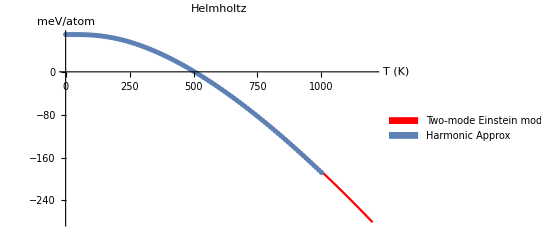

```mathematica
Show[Heinstein,Hqha]
```

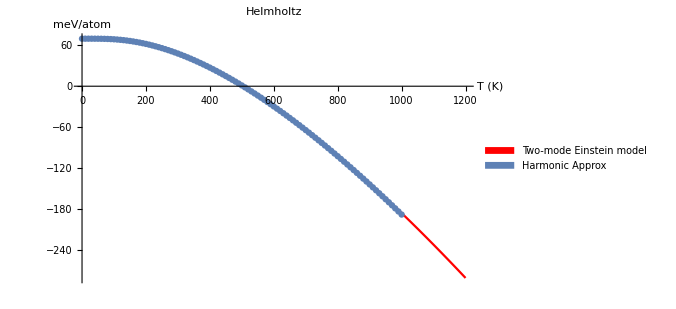

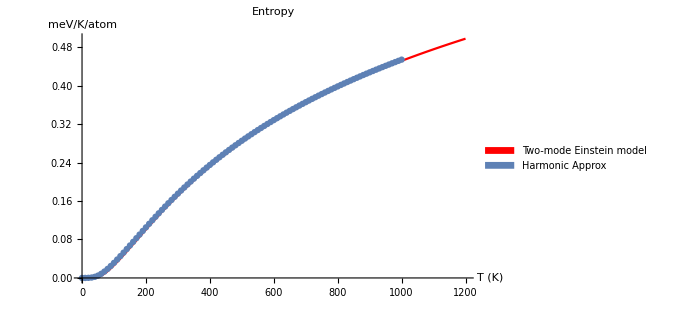

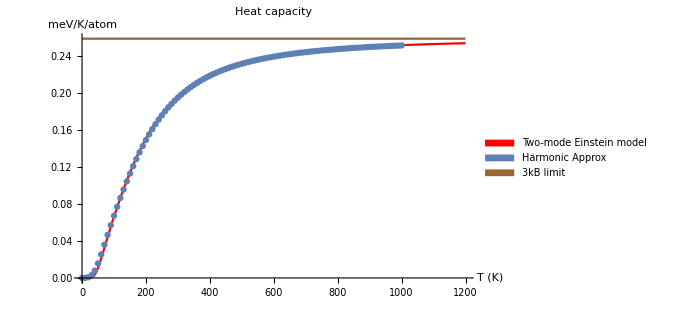

```mathematica
Show[Heinstein,Hqha,ImageSize->500]
Show[Seinstein,Sqha,ImageSize->500]
Show[Cveinstein,Cvqha,kBlimit,ImageSize->500]
Show[Eneinstein,Enqha];
```

```mathematica
(*Why can I not define thermodynamics functions in terms of the partition function??
1) In terms of the partition function product as in the phonopy website, or
2) In terms of the partition function as a sum? *)
"https://atztogo.github.io/phonopy/theory.html partition function";
FoldList[Times,cspectrum];
phonoPartition[T_,list_]:=Exp[-1/(K2meV*T)]*FoldList[Times,(Exp[-list/(2*K2meV*T)])/(1-Exp[-list/(K2meV*T)])][[1]];
```

FoldList::normal: Nonatomic expression expected at position 2 in FoldList[Times,cspectrum].

```mathematica
cspectrum[[1]]
zrspectrum[[1]]
```

Part::partd: Part specification cspectrum⟦1⟧ is longer than depth of object.

cspectrum⟦1⟧

Part::partd: Part specification zrspectrum⟦1⟧ is longer than depth of object.

zrspectrum⟦1⟧

```mathematica
freePhonon[T_,list_]:=-K2meV*T*phonoPartition[T,list]
Plot[1.5(freePhonon[T,cspectrum]+cspectrum[[1]]),{T,1,1000}]
Plot[1.5(freePhonon[T,zrspectrum]+zrspectrum[[1]]),{T,1,1000}]
Plot[1.5(freePhonon[T,zrspectrum]+zrspectrum[[1]]+freePhonon[T,cspectrum]+cspectrum[[1]]),{T,1,500}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Einstein4685[[2]]
spectrum=Table[0.5+i,{i,0,70}];
cspectrum=Einstein4685[[1]]*spectrum;
zrspectrum=Einstein4685[[2]]*spectrum;
fullspectrum=Join[cspectrum,zrspectrum];
helm2[T_]:=-K2meV*T*[Exp[-((fullspectrum)/(K2meV*T))]]

helm[1]
```

26.3295

```mathematica
Plot[helm[T],{T,1,1000}]
```

-Graphics-

```mathematica
ListPlot@Table[-D[helm[T],T]/.T->t,{t,10,4000,100}]
```

-Graphics-

```mathematica
D[helm[T],T]
```

helm'[T]